# PRACTICAL 3 : Plotting of third order solution family of differential equations

## Ques 1 : Solve third order DE dE and plot its any three solutions

Real and Distinct Roots

```mathematica
sol=DSolve[y'''[x]-5*y''[x]+8*y'[x]-4y[x]==0 , y[x], x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(2 x) x C[3]}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]-> 1, C[2]-> 2, C[3]-> 2/3}]
```

ⅇ^x+2 ⅇ^(2 x)+2/3 ⅇ^(2 x) x

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]-> 0.5, C[2]-> 2, C[3]-> 3}]
```

0.5 ⅇ^x+2 ⅇ^(2 x)+3 ⅇ^(2 x) x

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]-> -1, C[2]-> -2, C[3]-> 0.5}]
```

-ⅇ^x-2 ⅇ^(2 x)+0.5 ⅇ^(2 x) x

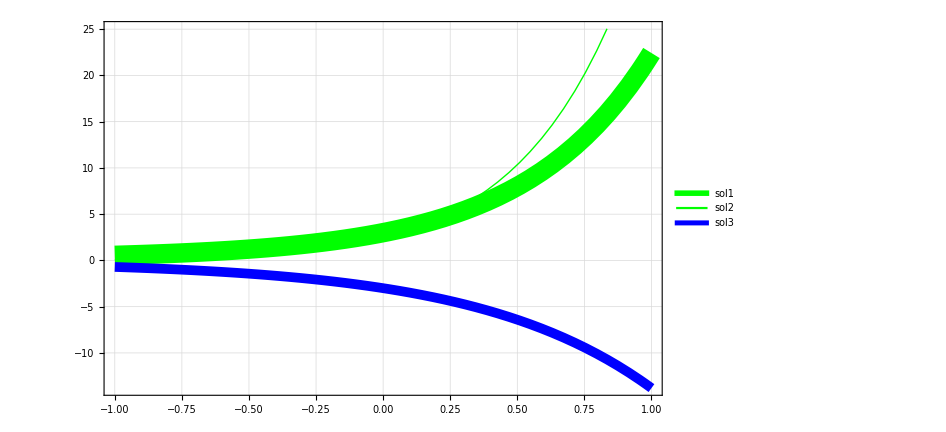

```mathematica
Plot[{sol1, sol2, sol3} , {x,-1,1}, ImageSize-> 700,PlotStyle->{{Green, Thickness[0.02]}, {Green, Thick}, {Blue, Thickness[0.01]}}, Frame->True, AxesOrigin->{0,0}, GridLines->Automatic, PlotLegends->Placed[LineLegend["Expressions", LegendLayout->"Column" , LegendFunction->"Frame"], {0.15, 0.87}]]
```

### Ques 2 :

{{y[x]→ⅇ^(-7 x) C[1]+ⅇ^x C[2]+ⅇ^(3 x) C[3]}}

ⅇ^(-7 x)+2 ⅇ^x+3 ⅇ^(3 x)

2 ⅇ^(-7 x)+4 ⅇ^x+8 ⅇ^(3 x)

-3 ⅇ^(-7 x)-2 ⅇ^x-4 ⅇ^(3 x)

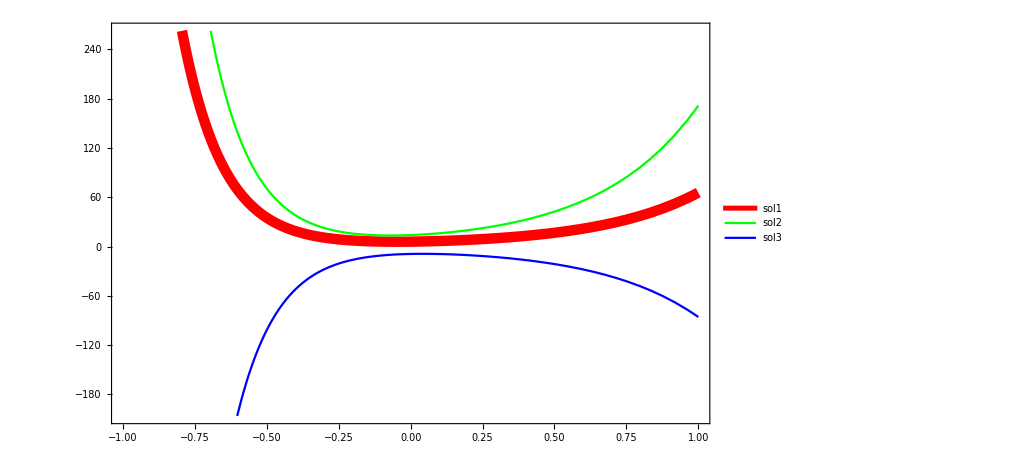

```mathematica
sol=DSolve[y'''[x]+3*y''[x]-25y'[x]+21*y[x]==0, y[x], x]
sol1=Evaluate[y[x]/. sol[[1]]/.{C[1]-> 1, C[2]-> 2, C[3]-> 3}]
sol2=Evaluate[y[x]/.sol[[1]]/. {C[1]-> 2, C[2]-> 4, C[3]-> 8}]
sol3=Evaluate[y[x]/.sol[[1]]/. {C[1]-> -3, C[2]-> -2, C[3]-> -4}]
Plot[{sol1, sol2, sol3},{x,-1,1}, PlotStyle->{{Red, Thickness[0.01]}, {Green, Thicker}, {Blue, thick}}, Frame->True, ImageSize->750, PlotLegends->Placed[{"sol1", "sol2", "sol3"}, Left]]
```

### Ques 3 :

### Ques 4 : Solve third order differential Equation and plot its any three solutions

```mathematica
sol=DSolve[y'''[x]-13*y''[x]+19*y'[x]+33*y[x]== Cos[2x] , y[x] ,x]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(11 x) C[3]+(17 Cos[2 x]+6 Sin[2 x])/1625}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]-> 1, C[2]-> 2, C[3]-> 3}]
```

ⅇ^-x+2 ⅇ^(3 x)+3 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]-> 2, C[2]-> 4, C[3]-> 8}]
```

2 ⅇ^-x+4 ⅇ^(3 x)+8 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]-> 3, C[2]-> 6, C[3]-> 9}]
```

3 ⅇ^-x+6 ⅇ^(3 x)+9 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

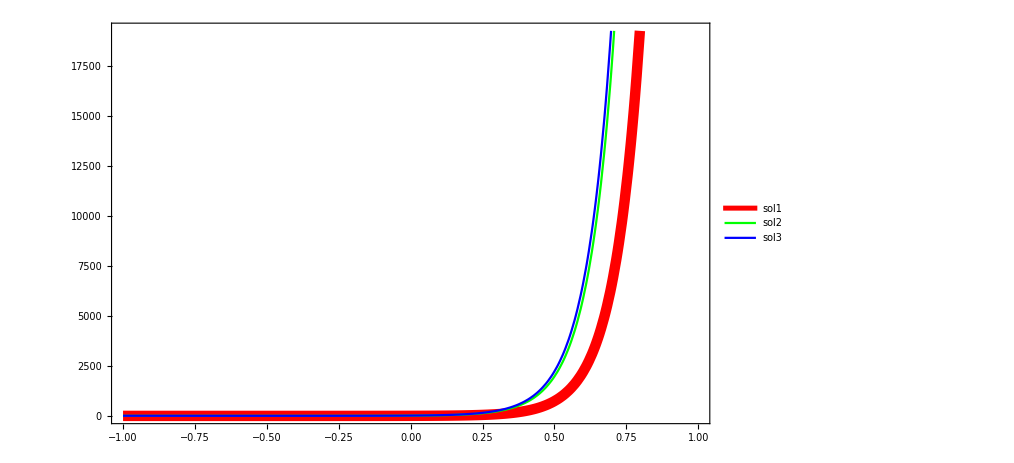

```mathematica
Plot[{sol1, sol2, sol3}, {x,-1,1}, PlotStyle->{{Red, Thickness[0.01]}, {Green, Thicker}, {Blue, thick}}, Frame->True, ImageSize->750, PlotLegends->Placed[{"sol1", "sol2", "sol3"}, Below]]
```

## Solve the following differential equations

### Q 1 . y’’’ -6y’’+5y’ + 12y = 0

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(4 x) C[3]}}

ⅇ^-x+2 ⅇ^(3 x)+3 ⅇ^(4 x)

2 ⅇ^-x+4 ⅇ^(3 x)+8 ⅇ^(4 x)

ⅇ^-x/3+ⅇ^(3 x)/2+(2 ⅇ^(4 x))/3

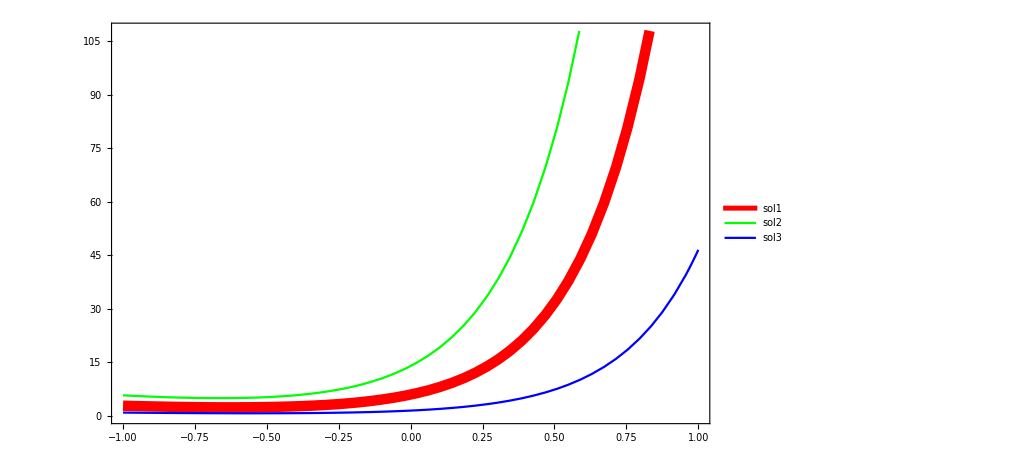

```mathematica
sol=DSolve[y'''[x]-6*y''[x]+5y'[x]+12*y[x]==0, y[x], x]
sol1=Evaluate[y[x]/. sol[[1]]/.{C[1]-> 1, C[2]-> 2, C[3]-> 3}]
sol2=Evaluate[y[x]/.sol[[1]]/. {C[1]-> 2, C[2]-> 4, C[3]-> 8}]
sol3=Evaluate[y[x]/.sol[[1]]/. {C[1]-> 1/3, C[2]-> 1/2, C[3]-> 2/3}]
Plot[{sol1, sol2, sol3},{x,-1,1}, PlotStyle->{{Red, Thickness[0.01]}, {Green, Thicker}, {Blue, thick}}, Frame->True, ImageSize->750, PlotLegends->Placed[{"sol1", "sol2", "sol3"}, Top]]
```

### Q2 . y’’’-6y’’+11y’ -6y=0, y(0)=0, y’(0)=0, y”(0)=2

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(3 x) C[3]}}

ⅇ^x+2 ⅇ^(2 x)+3 ⅇ^(3 x)

2 ⅇ^x+4 ⅇ^(2 x)+8 ⅇ^(3 x)

-3 ⅇ^x-2 ⅇ^(2 x)-4 ⅇ^(3 x)

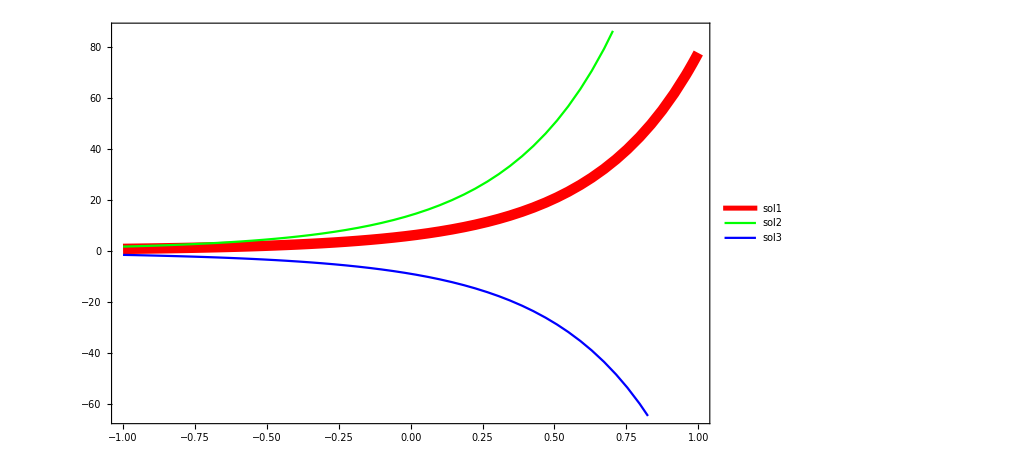

```mathematica
sol=DSolve[y'''[x]-6*y''[x]+11y'[x]-6*y[x]==0, y[x], x]
sol1=Evaluate[y[x]/. sol[[1]]/.{C[1]-> 1, C[2]-> 2, C[3]-> 3}]
sol2=Evaluate[y[x]/.sol[[1]]/. {C[1]-> 2, C[2]-> 4, C[3]-> 8}]
sol3=Evaluate[y[x]/.sol[[1]]/. {C[1]-> -3, C[2]-> -2, C[3]-> -4}]
Plot[{sol1, sol2, sol3},{x,-1,1}, PlotStyle->{{Red, Thickness[0.01]}, {Green, Thicker}, {Blue, thick}}, Frame->True, ImageSize->750, PlotLegends->Placed[{"sol1", "sol2", "sol3"}, Left]]
```

### Q3. y’’’ + y’ = sec x

{{y[x]→C[3]-x Cos[x]-C[2] Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+C[1] Sin[x]+Log[Cos[x]] Sin[x]}}

18-4.5 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+3 Sin[x]+Log[Cos[x]] Sin[x]

-1. Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+0.6 Sin[x]+Log[Cos[x]] Sin[x]

-2+3 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]-9 Sin[x]+Log[Cos[x]] Sin[x]

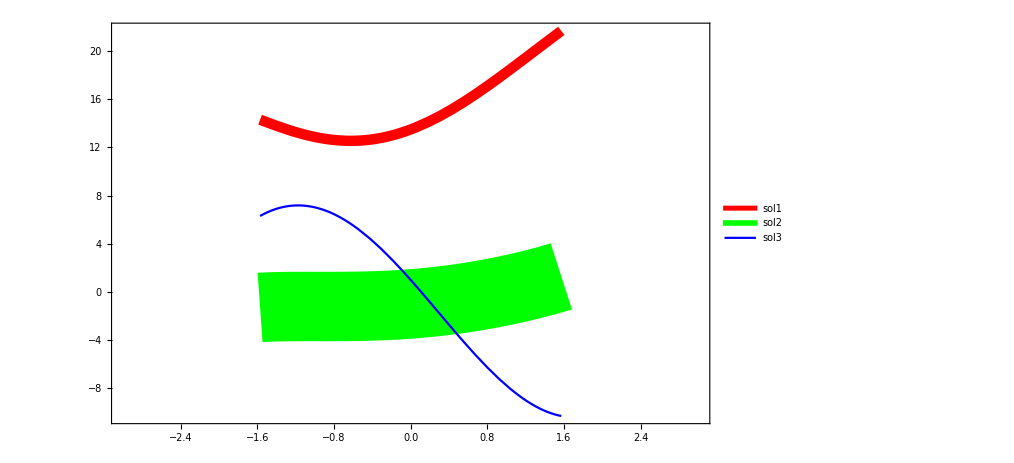

```mathematica
sol=DSolve[y'''[x]+0*y''[x]+y'[x]+0*y[x]==Sec[x], y[x], x]
sol1=Evaluate[y[x]/. sol[[1]]/.{C[1]-> 3, C[2]-> 4.5, C[3]-> 18}]
sol2=Evaluate[y[x]/.sol[[1]]/. {C[1]-> 0.6, C[2]-> 1.0, C[3]-> 0}]
sol3=Evaluate[y[x]/.sol[[1]]/. {C[1]-> -9, C[2]-> -3, C[3]-> -2}]
Plot[{sol1, sol2, sol3},{x,-3,3}, PlotStyle->{{Red, Thickness[0.01]}, {Green, Thickness[0.8]}, {Blue, thick}}, Frame->True, ImageSize->750, PlotLegends->Placed[{"sol1", "sol2", "sol3"}, Below]]
```